# Analisi Sistema LTI-TD

## Inizializzo le matrici A,B e C1

```mathematica
ClearAll["Global`*"]
```

```mathematica
A={{-92/125, -107/125, -43/50}, {217/125, -18/125, -7/50}, 
 {-184/125, 36/125, 7/25}};
B={{-1/2}, {1/2}, {-1}};
C1= {{9/4, -7/4, -2}};
```

Calcolo gli autovalori

```mathematica
λ= Eigenvalues[A]
```

{-1/5,-1/5,-1/5}

```mathematica
{T,Λ}=JordanDecomposition[A]
```

{{{3/26,-425/676,1125/8788},{-14/13,175/676,2875/4394},{1,0,0}},{{-1/5,1,0},{0,-1/5,1},{0,0,-1/5}}}

```mathematica
Λ // MatrixForm
```

(-1/5 | 1 | 0
0 | -1/5 | 1
0 | 0 | -1/5)

```mathematica
MatrixPower[Λ,k] // MatrixForm
```

((-1/5)^k | -(-1)^k 5^(1-k) k | 1/2 (-1)^k 5^(2-k) (-1+k) k
0 | (-1/5)^k | -(-1)^k 5^(1-k) k
0 | 0 | (-1/5)^k)

```mathematica
Subscript[x, 0]={{0},{0},{-3}}
```

{{0},{0},{-3}}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{{-3},{-36/25},{-546/125}}

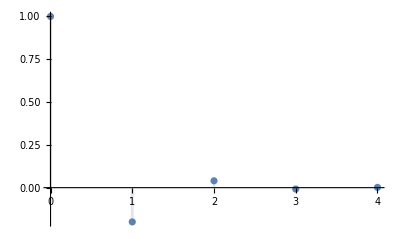

```mathematica
DiscretePlot[(-1/5)^k,{k,0,4},PlotRange->All]
```

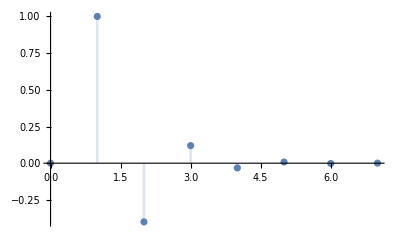

```mathematica
DiscretePlot[Binomial[k,1](-1/5)^(k-1),{k,0,7},PlotRange->All]
```

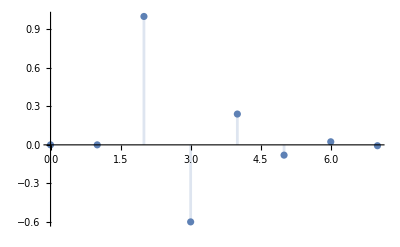

```mathematica
DiscretePlot[Binomial[k,2](-1/5)^(k-2),{k,0,7},PlotRange->All]
```

### Calcolo la risposta libera

```mathematica
Subscript[x, l][k_]:=Simplify[T.MatrixPower[Λ,k].Subscript[z, 0]]
Subscript[x, l][k]
```

{{-3/2 (-1)^k 5^(-1-k) k (22+21 k)},{21/2 (-1)^k 5^(-1-k) k (-29+28 k)},{-3 (-1)^k 5^(-1-k) (5-103 k+91 k^2)}}

```mathematica
Subscript[y, l][k_]:=Simplify[C1.Subscript[x, l][k]]
Subscript[y, l][k]
```

{{-3/8 (-1/5)^k (-16+85 k+21 k^2)}}

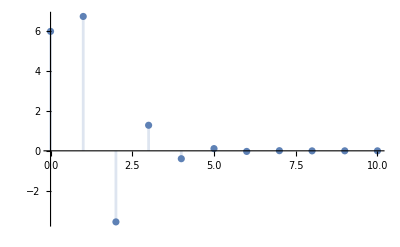

```mathematica
DiscretePlot[Evaluate[Subscript[y, l][k]],{k,0,10},PlotRange->All]
```

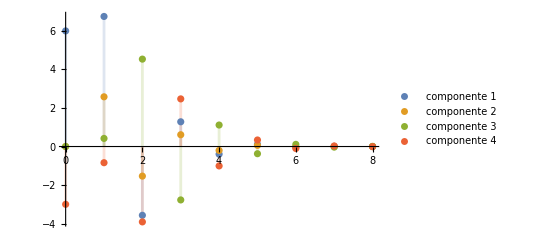

```mathematica
DiscretePlot[{Evaluate[Subscript[y, l][k]], Evaluate[Subscript[x, l][k]]},{k,0,8},PlotRange->All, PlotLegends-> {"componente 1","componente 2","componente 3", "componente 4"}]
```

### “Accendiamo” i modi naturali

{3/26,-14/13,1}

{1,0,0}

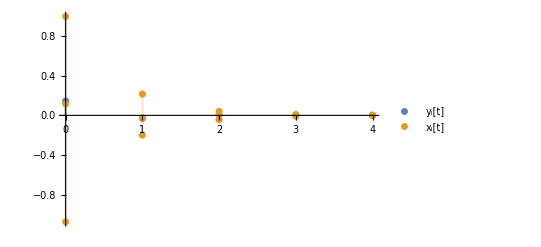

```mathematica
Subscript[x, 0]=Transpose[T][[1]]
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
DiscretePlot[{Subscript[y, l][t],Subscript[x, l][t]},{t,0,4},PlotRange->All, PlotLegends->{"y_l[t]","x_l[t]"}]
```

{-425/676,175/676,0}

{0,1,0}

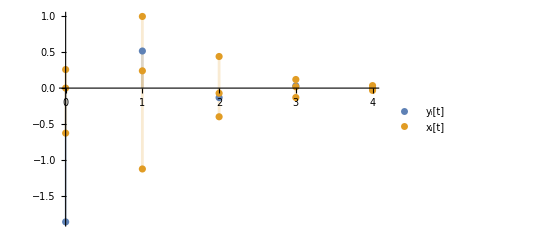

```mathematica
Subscript[x, 0]=Transpose[T][[2]]
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
DiscretePlot[{Subscript[y, l][t],Subscript[x, l][t]},{t,0,4},PlotRange->All, PlotLegends->{"y_l[t]","x_l[t]"}]
```

{1125/8788,2875/4394,0}

{0,0,1}

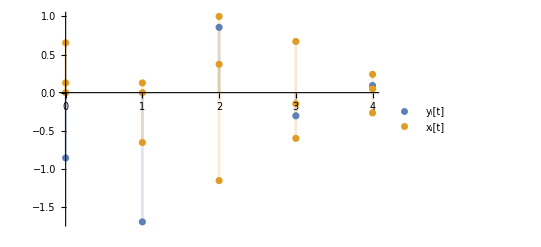

```mathematica
Subscript[x, 0]=Transpose[T][[3]]
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
DiscretePlot[{Subscript[y, l][t],Subscript[x, l][t]},{t,0,4},PlotRange->All, PlotLegends->{"y_l[t]","x_l[t]"}]
```

Primi due modi:

```mathematica
T // MatrixForm
```

(3/26 | -425/676 | 1125/8788
-14/13 | 175/676 | 2875/4394
1 | 0 | 0)

{-1100/2197,8025/8788,0}

{0,1,1}

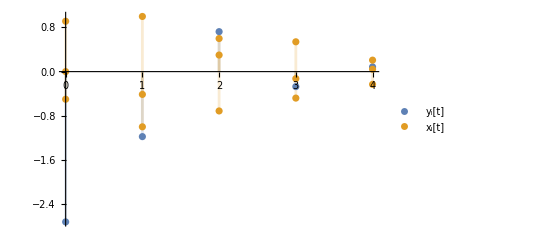

```mathematica
Subscript[x, 0]= T[[All,2]]1+T[[All,3]]1
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
DiscretePlot[{Subscript[y, l][t],Subscript[x, l][t]},{t,0,4},PlotRange->All, PlotLegends->{"y_l[t]","x_l[t]"}]
```

{2139/8788,-1857/4394,1}

{1,0,1}

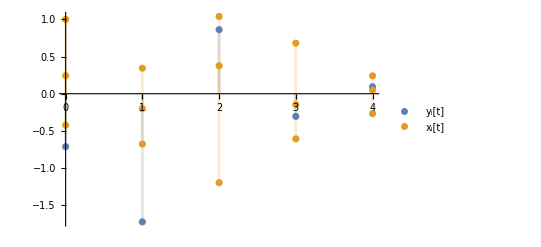

```mathematica
Subscript[x, 0]= T[[All,1]]1+T[[All,3]]1
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
DiscretePlot[{Subscript[y, l][t],Subscript[x, l][t]},{t,0,4},PlotRange->All, PlotLegends->{"y_l[t]","x_l[t]"}]
```

### calcolo la FdT a partire dalla definizione

```mathematica
G[z_]:=Simplify[C1.Inverse[z IdentityMatrix[3]-A].B][[1]][[1]]
```

```mathematica
G[z]
```

(125 (1+8 z))/(4 (1+5 z)^3)

#### Calcolo poli e zeri

```mathematica
Solve[Denominator[G[z]]==0,z]
```

{{z→-1/5},{z→-1/5},{z→-1/5}}

```mathematica
Solve[Numerator[G[z]]==0,z]
```

{{z→-1/8}}

```mathematica
Σ=StateSpaceModel[{A,B,C1},SamplingPeriod->1]
```

-92/125-107/125-43/50-1/2217/125-18/125-7/501/2-184/12536/1257/25-19/4-7/4-201StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1131FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionModel[Σ]
```

(-1/4-2 z)/(-1/125-(3 z)/25-(3 z^2)/5-z^3)1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#z11-1-11FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionPoles[Σ]
```

{{{-1/5,-1/5,-1/5}}}

```mathematica
TransferFunctionZeros[Σ]
```

{{{-1/8}}}

```mathematica
{{{-1/8}}}
```

{{{-1/8}}}

## Risposta al gradino unitario

```mathematica
Subscript[Y, f][z_]:=G[z](z/(z-1))
Factor[(Subscript[Y, f][z])/z]
```

(125 (1+8 z))/(4 (-1+z) (1+5 z)^3)

```mathematica
Subscript[C, 1](1/(z-1))+Subscript[C, 21](1/(z+1/5))+Subscript[C, 22](1/(z+1/5)^2)+Subscript[C, 23](1/(z+1/5)^3)
```

125/(96 (-1+z))+1/(8 (1/5+z)^3)-25/(16 (1/5+z)^2)-125/(96 (1/5+z))

```mathematica
Subscript[C, 1]=lim_(z->1) (z-1)((Subscript[Y, f][z])/z)
```

125/96

Heaviside generalizzata

```mathematica
Subscript[C, 23]=lim_(z->-1/5) (z+1/5)^3((Subscript[Y, f][z])/z)
```

1/8

```mathematica
Subscript[C, 22]=lim_(z->-1/5) D[(z+1/5)^3((Subscript[Y, f][z])/z),z]
```

-25/16

```mathematica
Subscript[C, 21]=(1/2)lim_(z->-1/5) D[D[(z+1/5)^3((Subscript[Y, f][z])/z),z],z]
```

-125/96

```mathematica
Subscript[C, 1](z/(z-1))+Subscript[C, 21](z/(z+1/5))+Subscript[C, 22](z/(z+1/5)^2)+Subscript[C, 23](z/(z+1/5)^3)
```

### Risposta forzata nel dominio del tempo

```mathematica
Subscript[y, f][k_]:=Subscript[C, 1] UnitStep[k]+Subscript[C, 21](-1/5)^k UnitStep[k]+Subscript[C, 22] Binomial[k,1](-1/5)^(k-1)UnitStep[k]+
Subscript[C, 23] Binomial[k,2](-1/5)^(k-2)UnitStep[k]
```

```mathematica
Subscript[y, ss][k_]:=Subscript[C, 1] UnitStep[k]
Subscript[y, tr][k_]:=Subscript[C, 21](-1/5)^k UnitStep[k]+Subscript[C, 22] Binomial[k,1](-1/5)^(k-1)UnitStep[k]+
Subscript[C, 23] Binomial[k,2](-1/5)^(k-2)UnitStep[k]
```

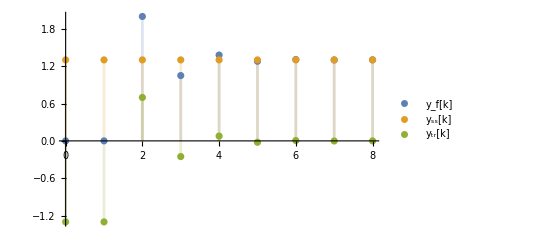

```mathematica
DiscretePlot[{Evaluate[Subscript[y, f][k]],Evaluate[Subscript[y, ss][k]],Evaluate[Subscript[y, tr][k]]},
{k,0,8},PlotRange->All,PlotLegends->{"y_f[k]","y_ss[k]","y_tr[k]"}]
```

## Modello ARMA

```mathematica
Subscript[x, 0]={{0},{-2},{-3}}
```

{{0},{-2},{-3}}

```mathematica
Subscript[y, 0]={{Subscript[y, 1]},{Subscript[y, 2]},{Subscript[y, 3]}}
```

{{19/2},{45/4},{-2959/500}}

```mathematica
Subscript[y, 1]= FullSimplify[C1.Subscript[x, 0]][[1]][[1]]
```

19/2

```mathematica
Subscript[y, 2]=FullSimplify[C1.A.Subscript[x, 0]][[1]][[1]]
```

45/4

```mathematica
Subscript[y, 3]=FullSimplify[C1.A.A.Subscript[x, 0]][[1]][[1]]
```

-2959/500

```mathematica
Subscript[y, 0]
```

{{19/2},{45/4},{-2959/500}}

```mathematica
Intedita= Expand[Denominator[G[z]]*Y[z]]== Expand[Numerator[G[z]]U[z]]
```

4 Y[z]+60 z Y[z]+300 z^2 Y[z]+500 z^3 Y[z]==125 U[z]+1000 z U[z]

```mathematica
Ricorrenza=Intedita/.{Y[z]->y[k],z Y[z]->y[k+1],z^2 Y[z]->y[k+2],z^3 Y[z]->y[k+3],U[z]->u[k],z U[z]->u[k+1]}
```

4 y[k]+60 y[1+k]+300 y[2+k]+500 y[3+k]==125 u[k]+1000 u[1+k]

```mathematica
Ricorrenza=(ZTransform[Ricorrenza,k,z])/.{ZTransform[y[k],k,z]->Y[z],ZTransform[u[k],k,z]->U[z],u[0]->0};
```

```mathematica
(*Adesso vado a risovlere l'equazione differenziale, ottenendo la risposta del sistema nel dominio della trasformata Z*)
```

```mathematica
Risposta=Collect[Solve[Ricorrenza, Y[z]][[1,1]][[2]], U[z]]
```

(5 (25+200 z) U[z])/(4 (1+5 z)^3)+(5 (12 z y[0]+60 z^2 y[0]+100 z^3 y[0]+60 z y[1]+100 z^2 y[1]+100 z y[2]))/(4 (1+5 z)^3)

```mathematica
RispostaLibera = 1/(4 (1+5 z)^3)5 (12 z y[0]+60 z^2 y[0]+100 z^3 y[0]+60 z y[1]+100 z^2 y[1]+100 z y[2])
```

(5 (12 z y[0]+60 z^2 y[0]+100 z^3 y[0]+60 z y[1]+100 z^2 y[1]+100 z y[2]))/(4 (1+5 z)^3)

```mathematica
(*Determino la risposta libera,sfruttando i valori appena calcolati*)
```

```mathematica
RispostaLibera = (1/(4 (1+5 z)^3)5 (12 z y[0]+60 z^2 y[0]+100 z^3 y[0]+60 z y[1]+100 z^2 y[1]+100 z y[2]))/.
{y[0] -> Subscript[y, 0][[1,1]], y[1]-> Subscript[y, 0][[2,1]], y[2]->Subscript[y, 0][[3,1]]}
```

(5 ((986 z)/5+1695 z^2+950 z^3))/(4 (1+5 z)^3)

```mathematica
RispostaLiberaConfronto =Simplify[ C1.Inverse[z IdentityMatrix[3]-A].Subscript[x, 0]][[1,1]]
```

(986+8475 z+4750 z^2)/(4 (1+5 z)^3)

```mathematica
(*Come si può vedere i due valori coincidono, allora ho trovato un modello ARMA equivalente. l'equivalenza tra le due rappresentazioni conferma la correttezza del calcolo delle condizioni iniziali, e di conseguenza della risposta libera del sistema. *)
```

## Risposta all’ingresso u(k)

```mathematica
(* definisco il mio ingresso*)
```

```mathematica
Subscript[U, pw][z]= ∑_(k=0)^10 z^-k
```

1+1/z^10+1/z^9+1/z^8+1/z^7+1/z^6+1/z^5+1/z^4+1/z^3+1/z^2+1/z

```mathematica
Subscript[Y, pw][z]= Risposta /. {U[z]->Subscript[U, pw][z], y[0]->Subscript[y, 1],y[1]->Subscript[y, 2],y[2]->Subscript[y, 3]}
```

(5 (1+1/z^10+1/z^9+1/z^8+1/z^7+1/z^6+1/z^5+1/z^4+1/z^3+1/z^2+1/z) (25+200 z))/(4 (1+5 z)^3)+(5 ((986 z)/5+1695 z^2+950 z^3))/(4 (1+5 z)^3)

```mathematica
(*effettuo l'antitrasformata*)
```

```mathematica
Subscript[y, pw][k_]:= InverseZTransform[Subscript[Y, pw][z],z,k]
```

```mathematica
Subscript[y, pw][k]
```

1/4 (-1)^k 5^(-1-k) (116221110190-27465821243 k+1525878678 k^2) (1-UnitStep[10-k])+(50856237 UnitStep[10-k] UnitStep[-10+k])/39062500+(50889329 UnitStep[9-k] UnitStep[-9+k])/39062500+(5075319 UnitStep[8-k] UnitStep[-8+k])/3906250+(2052039 UnitStep[7-k] UnitStep[-7+k])/1562500+(78653 UnitStep[6-k] UnitStep[-6+k])/62500+(3663 UnitStep[5-k] UnitStep[-5+k])/2500+(4533 UnitStep[4-k] UnitStep[-4+k])/6250+(7937 UnitStep[3-k] UnitStep[-3+k])/2500-1959/500 UnitStep[2-k] UnitStep[-2+k]+45/4 UnitStep[1-k] UnitStep[-1+k]+(19 UnitStep[-k])/2

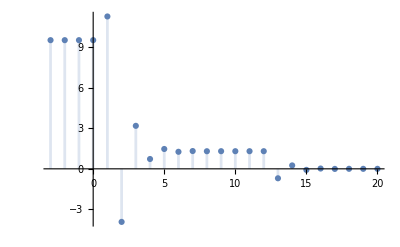

```mathematica
DiscretePlot[Evaluate[Subscript[y, pw][k]],{k,-3,20},PlotRange->All]
```

```mathematica
(*risposta forzata*)
```

```mathematica
Subscript[y, fpw][k_]:= InverseZTransform[1/(4 (1+5 z)^3)5 (1+1/z^10+1/z^9+1/z^8+1/z^7+1/z^6+1/z^5+1/z^4+1/z^3+1/z^2+1/z) (25+200 z),z,k]
```

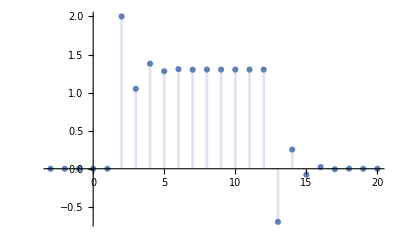

```mathematica
DiscretePlot[Evaluate[Subscript[y, fpw][k]],{k,-3,20},PlotRange->All]
```

## Condizioni Iniziali ARMA

```mathematica
y0={{Subscript[y, 11]},{Subscript[y, 22]},{Subscript[y, 33]}}
x0 = {{Subscript[x, 11]},{Subscript[x, 22]},{Subscript[x, 33]}}
```

{{y_11},{y_22},{y_33}}

{{x_11},{x_22},{x_33}}

```mathematica
U[z]= ZTransform[UnitStep[k],k,z]
```

z/(-1+z)

```mathematica
RispostaCI= ((5 (25+200 z) U[z])/(4 (1+5 z)^3)+1/(4 (1+5 z)^3)5 (12 z y[0]+60 z^2 y[0]+100 z^3 y[0]+60 z y[1]+100 z^2 y[1]+100 z y[2]))/.{y[0]->Subscript[y, 11],y[1]->Subscript[y, 22],y[2]->Subscript[y, 33]}
```

(5 z (25+200 z))/(4 (-1+z) (1+5 z)^3)+(5 (12 z y_11+60 z^2 y_11+100 z^3 y_11+60 z y_22+100 z^2 y_22+100 z y_33))/(4 (1+5 z)^3)

```mathematica
(* divido le componenti *)
Rlibera= (5 (12 z Subscript[y, 11]+60 z^2 Subscript[y, 11]+100 z^3 Subscript[y, 11]+60 z Subscript[y, 22]+100 z^2 Subscript[y, 22]+100 z Subscript[y, 33]))/(4 (1+5 z)^3)
Rforzata= (5 z (25+200 z))/(4 (-1+z) (1+5 z)^3)
Rregime=  (G[1]z)/(z-1)
Rtransitoria = Factor[Rforzata-Rregime]
```

(5 (12 z y_11+60 z^2 y_11+100 z^3 y_11+60 z y_22+100 z^2 y_22+100 z y_33))/(4 (1+5 z)^3)

(5 z (25+200 z))/(4 (-1+z) (1+5 z)^3)

(125 z)/(96 (-1+z))

-(125 z (23+200 z+125 z^2))/(96 (1+5 z)^3)

```mathematica
(* azzero libera+transitoria*)
```

```mathematica
Numerator[Simplify[Expand[Rlibera+Rtransitoria]]]
```

5 z (96 (3+15 z+25 z^2) y_11+480 (3+5 z) y_22-25 (23+200 z+125 z^2-96 y_33))

```mathematica
CoefficientList[Numerator[Simplify[Expand[Rlibera+Rtransitoria]]],z]
```

{0,-2875+1440 y_11+7200 y_22+12000 y_33,-25000+7200 y_11+12000 y_22,-15625+12000 y_11}

```mathematica
Solve[CoefficientList[Numerator[Simplify[Expand[Rlibera+Rtransitoria]]],z]=={0,0,0,0},{Subscript[y, 11],Subscript[y, 22],Subscript[y, 33]}]
```

{{y_11→125/96,y_22→125/96,y_33→-67/96}}

```mathematica
Ob = {{C1}[[1,1]],{C1.A}[[1,1]],{C1.A.A}[[1,1]]}
```

{{9/4,-7/4,-2},{-7/4,-9/4,-9/4},{347/500,587/500,119/100}}

```mathematica
y0= {{125/96},{125/96},{-67/96}}
```

{{125/96},{125/96},{-67/96}}

```mathematica
x0= Inverse[Ob].y0
```

{{0},{125/216},{-125/108}}